```mathematica
Data={{1,2},{2,3},{3,5}};
```

## Natural Spline Module

```mathematica
NaturalSpline[Data_]:=Module[{h,a,L,U,Diag,M,B,c,b,d,Poly,P},
h[n_]:=Data[[n+1]][[1]]-Data[[n]][[1]];
a=Table[Data[[i]][[2]],{i,1,Length[Data]}];
L=DiagonalMatrix[Table[h[i],{i,1,Length[Data]-2}]~Join~{0},-1];
U=DiagonalMatrix[{0}~Join~Table[h[i],{i,2,Length[Data]-1}],1];
Diag=DiagonalMatrix[{1}~Join~Table[2(h[i]+h[i+1]),{i,1,Length[Data]-2}]~Join~{1}];
M=L+U+Diag;
B={0}~Join~Table[(3/h[i+1])(a[[i+2]]-a[[i+1]])-(3/h[i])(a[[i+1]]-a[[i]]),{i,1,Length[Data]-2}]~Join~{0};
c=LinearSolve[M,B];
b=Table[(1/h[i])(a[[i+1]]-a[[i]])-(h[i]/3)(2c[[i]]+c[[i+1]]),{i,1,Length[Data]-1}];
d=Table[(c[[i+1]]-c[[i]])/(3h[i]),{i,1,Length[Data]-1}];
Poly=Table[a[[i]]+b[[i]](x-Data[[i]][[1]])+c[[i]](x-Data[[i]][[1]])^2+d[[i]](x-Data[[i]][[1]])^3,{i,1,Length[Data]-1}];
P=Piecewise[Table[{Poly[[i]],Data[[i]][[1]]≤x≤Data[[i+1]][[1]]},{i,1,Length[Data]-1}]]
]
```

```mathematica
p=NaturalSpline[Data]
```

Piecewise[{{2+3/4 (-1+x)+1/4 (-1+x)^3, 1≤x≤2}, {3+3/2 (-2+x)+3/4 (-2+x)^2-1/4 (-2+x)^3, 2≤x≤3}, {0, True}}]

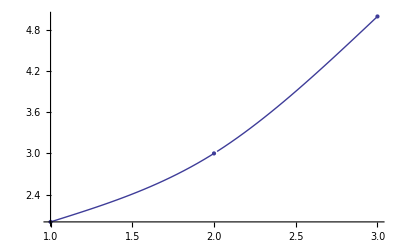

```mathematica
Show[{ListPlot[Data],Plot[p,{x,Data[[1,1]],Last[Data][[1]]}]}]
```

## Clamped Spline Module

```mathematica
ClampedSpline[Data_,fp_]:=Module[{h,a,L,U,Diag,M,B,c,b,d,PolyClamp,PClamp},
h[n_]:=Data[[n+1]][[1]]-Data[[n]][[1]];
a=Table[Data[[i]][[2]],{i,1,Length[Data]}];
L=DiagonalMatrix[Table[h[i],{i,1,Length[Data]-2}]~Join~{h[Length[Data]-1]},-1];
U=DiagonalMatrix[{h[1]}~Join~Table[h[i],{i,2,Length[Data]-1}],1];
Diag=DiagonalMatrix[{2*h[1]}~Join~Table[2(h[i]+h[i+1]),{i,1,Length[Data]-2}]~Join~{2*h[Length[Data]-1]}];
M=L+U+Diag;
B={(3/h[1]*(a[[2]]-a[[1]])-3*fp[[1]])}~Join~Table[(3/h[i+1])(a[[i+2]]-a[[i+1]])-(3/h[i])(a[[i+1]]-a[[i]]),{i,1,Length[Data]-2}]~Join~{3*fp[[2]]-((3/h[Length[Data]-1])*(a[[Length[Data]]]-a[[Length[Data]-1]]))};
c=LinearSolve[M,B];
b=Table[((a[[i+1]]-a[[i]])/h[i])-(h[i]*(c[[i+1]]+2*c[[i]])/3),{i,1,Length[Data]-1}];
d=Table[(c[[i+1]]-c[[i]])/(3h[i]),{i,1,Length[Data]-1}];
PolyClamp=Table[a[[i]]+b[[i]](x-Data[[i]][[1]])+c[[i]](x-Data[[i]][[1]])^2+d[[i]](x-Data[[i]][[1]])^3,{i,1,Length[Data]-1}];
PClamp=Piecewise[Table[{PolyClamp[[i]],Data[[i]][[1]]≤x≤Data[[i+1]][[1]]},{i,1,Length[Data]-1}]]
]
```

```mathematica
fp={2,1};
pclamp=ClampedSpline[Data,fp]
```

Piecewise[{{2+2 (-1+x)-5/2 (-1+x)^2+3/2 (-1+x)^3, 1≤x≤2}, {3+3/2 (-2+x)+2 (-2+x)^2-3/2 (-2+x)^3, 2≤x≤3}, {0, True}}]

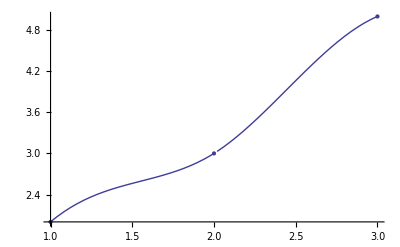

```mathematica
Show[{ListPlot[Data],Plot[pclamp,{x,Data[[1,1]],Last[Data][[1]]}]}]
```